```mathematica
F[x_]:=F[x]=x NIntegrate[BesselK[5/3,z],{z,x,∞}]
G[x_]:=x BesselK[2/3,x]
plot=Plot[F[x],{x,0,10}];
```

```mathematica
points=Cases[Cases[InputForm[plot],Line[___],Infinity],{_?NumericQ,_?NumericQ},Infinity];
x0=Select[points,#[[1]]<=.6&][[All,1]];
x1=Table[x,{x,2.0408163265306121*^-7,8,0.003}];
x2=Table[x,{x,8,50,.5}];
xval=Join[x1,x2];
len=Length@xval;
```

```mathematica
Monitor[fval=Table[{xval[[i]],F[xval[[i]]]},{i,1,len}],ProgressIndicator[i/len]]
Monitor[gval=Table[{xval[[i]],G[xval[[i]]]},{i,1,len}],ProgressIndicator[i/len]]
```

{{2.04082×10^-7,0.0126551},{0.0030002,0.304581},{0.0060002,0.379719},{0.0090002,0.430805},2745,{49.,4.66961×10^-21},{49.5,2.84625×10^-21},{50.,1.73479×10^-21}}
 |  |  |  |

{{2.04082×10^-7,0.00632773},{0.0030002,0.154933},{0.0060002,0.195054},{0.0090002,0.223082},2745,{49.,4.60873×10^-21},{49.5,2.80951×10^-21},{50.,1.7126×10^-21}}
 |  |  |  |

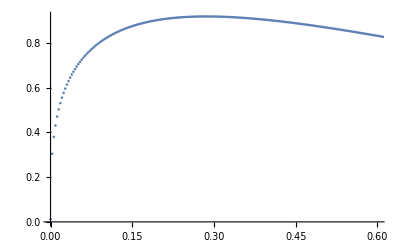

```mathematica
ListPlot[fval,PlotRange->{{0,.6},All}]
```

```mathematica
Export["C:\\Users\\Sjoerd\\Desktop\\tabel.txt",{#,CountryData[#,"GDP"]}&/@CountryData["G8"],"Table","FieldSeparators"->" "]
```

```mathematica
xvals="1.D-15,1.D-12,1.D-9,1.D-7,1.D-5,
     & 1.D-4,2.D-4,5.D-4,1.D-3,2.D-3,5.D-3,1.D-2,2.D-2,
     & 3.D-2,4.D-2,5.D-2,6.D-2,7.D-2,8.D-2,9.D-2,1.D-1,1.1D-1,
     & 1.2D-1,1.30D-1,1.4D-1,1.5D-1,1.6D-1,1.7D-1,1.8D-1,1.9D-1,2.D-1,
     & 2.1D-1,2.2D-1,2.3D-1,2.4D-1,2.5D-1,2.6D-1,2.7D-1,2.8D-1,2.9D-1,
     & 3.D-1,3.1D-1,3.2D-1,3.3D-1,3.4D-1,3.5D-1,3.6D-1,3.7D-1,3.8D-1,
     & 3.9D-1,4.D-1,4.1D-1,4.2D-1,4.3D-1,4.4D-1,4.5D-1,4.6D-1,4.7D-1,
     & 4.8D-1,4.9D-1,5.D-1,5.2D-1,5.4D-1,5.6D-1,5.8D-1,6.D-1,6.2D-1,
     & 6.4D-1,6.6D-1,6.8D-1,7.D-1,7.2D-1,7.4D-1,7.6D-1,7.8D-1,8.D-1,
     & 8.2D-1,8.4D-1,8.6D-1,8.8D-1,9.D-1,9.2D-1,9.4D-1,9.6D-1,9.8D-1,
     & 1.D0,1.05D0,1.1D0,1.15D0,1.2D0,1.25D0,1.3D0,1.35D0,1.4D0,1.45D0,
     & 1.5D0,1.55D0,1.6D0,1.65D0,1.7D0,1.75D0,1.8D0,1.85D0,1.9D0,
     & 1.95D0,2.D0,2.1D0,2.2D0,2.3D0,2.4D0,2.5D0,2.6D0,2.7D0,2.8D0,
     & 2.9D0,3.D0,3.1D0,3.2D0,3.3D0,3.4D0,3.5D0,3.6D0,3.7D0,3.8D0,
     & 3.9D0,4.D0,4.1D0,4.2D0,4.3D0,4.4D0,4.5D0,4.6D0,4.7D0,4.8D0,
     & 4.9D0,5.D0,5.25D0,5.5D0,5.75D0,6.D0,6.25D0,6.5D0,6.75D0,7.D0,
     & 7.25D0,7.5D0,7.75D0,8.D0,8.25D0,8.5D0,8.75D0,9.D0,9.25D0,9.5D0,
     & 9.75D0,1.D1,1.2D1,1.4D1,1.6D1,1.8D1,2.D1,2.5D1,3.D1,4.D1,5.D1/";
```

```mathematica
xval=ToExpression[StringReplace["{"<>StringDelete[xvals,{"&","\t","\n"," ","/"}]<>"}","D"->"*10^"]];
len=Length@xval;
```

```mathematica
Monitor[fval=Quiet@Table[{xval[[i]],F[xval[[i]]]},{i,1,len}],ProgressIndicator[i/len]];
Monitor[gval=Quiet@Table[{xval[[i]],G[xval[[i]]]},{i,1,len}],ProgressIndicator[i/len]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["G_vals.dat",gval,"Table","FieldSeparators"->" "]
```

/Users/pablogsal/PycharmProjects/HADES/integral_data

G_vals.dat